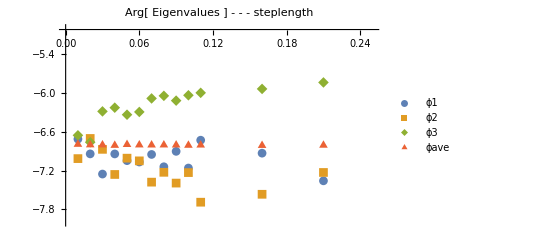

```mathematica
(*
running in the cluster:ne=4, 1000 50000 30 1
taking inverse/no inverse/single state plot.
*)
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - steplength",PlotRange->{{0,0.25},{-8,-5}}]
```

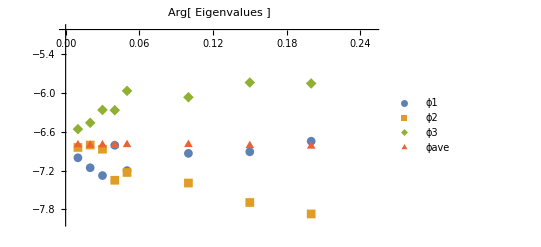

```mathematica
(*
running in the cluster:ne=4, 1000 50000 30 1
taking inverse/no inverse/single state plot.
*)
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength2","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ]",PlotRange->{{0,0.25},{-8,-5}}]
```

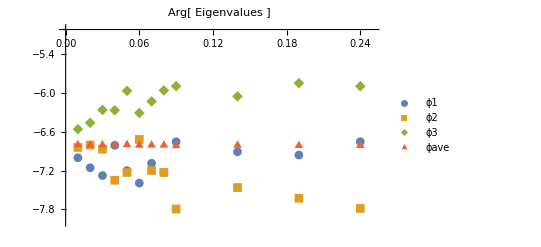

```mathematica
(*
running in the cluster:ne=4, 1000 50000 30 1
taking inverse/no inverse/single state plot.
*)
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength3","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ]",PlotRange->{{0,0.25},{-8,-5}}]
```

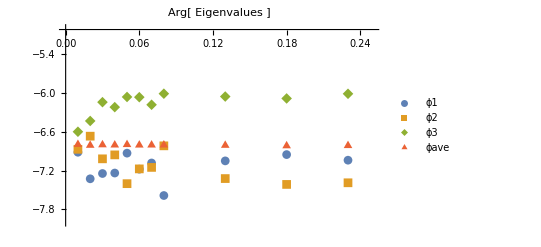

```mathematica
(*
running in the cluster:ne=4, 1000 50000 30 1
taking inverse/no inverse/single state plot.
*)
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength4","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ]",PlotRange->{{0,0.25},{-8,-5}}]
```

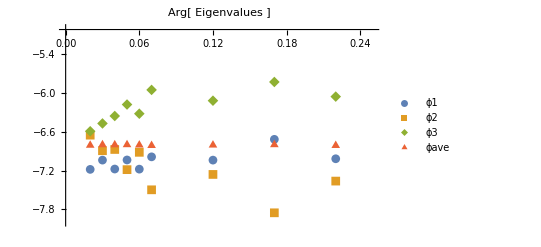

```mathematica
(*
running in the cluster:ne=4, 1000 50000 30 1
taking inverse/no inverse/single state plot.
*)
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength5","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ]",PlotRange->{{0,0.25},{-8,-5}}]
```